## Introduction

Sync state:

1. R global (d)
2. R global (σ)
3. C(v, v)(r)
4. C(v, v)(t)
5. C(θ, θ)(t) 
6. Look for clusters.... ? No, we don’t study periodic effects. Stick to what we study

## Main -- animation

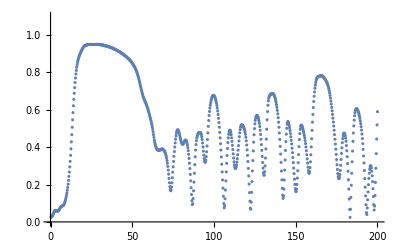

```mathematica
SeedRandom[1];
{dt,T,n}={0.25,200,300};
{J,k,σ}={1,1,10};
{R,L,d}={1,5,0};
{Ω}={1};
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=ω-Mean[ω];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
results={};Dynamic[results]
{t,NT}={0,Round[T/dt]};
{Zs,sols,ts}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];AppendTo[Zs,Z];
z0=znew;t++;AppendTo[ts,t*dt];
results=plotResults[znew,3];
];
ListPlot[{ts,Abs[Zs]}ᵀ,PlotRange->{0,1.1}]
```

#### Temp

## States

### Vary d

```mathematica
plotLocal[z_,L_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text["d = 1",{2.5,2.5}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];
Return[p1];
];

run[d_]:=Block[{dt,T,n,J,k,σ,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff},
{dt,T,n}={0.1,100,300};
{J,k,σ}={1,1,10};
{R,L,Ω}={1,5,0.1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[znew];
];
```

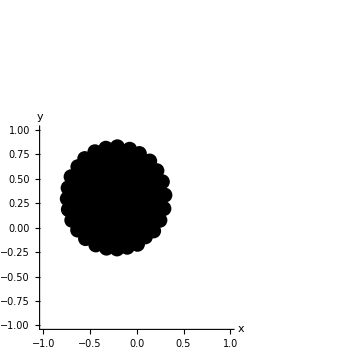

```mathematica
ds=Table[d,{d,0,1,0.2}];
dataZd=ParallelTable[run[d],{d,ds}];
```

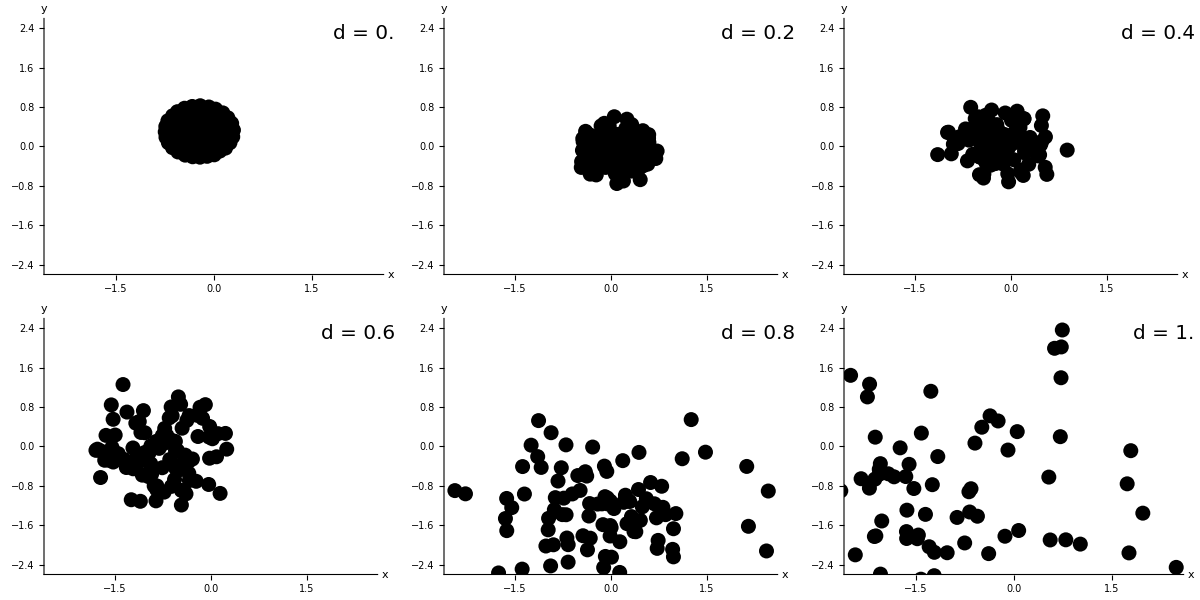

```mathematica
plotLocal[z_,L_,d_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text[Style["d = "<>ToString[d],20],{2.3,2.3}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->19];
Return[p1];
];
plots=Table[plotLocal[dataZd[[i]],2.5,ds[[i]]],{i,1,Length[ds]}];
p1=Grid[Partition[plots,3]]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-states-different-d.png",p1];
```

### Vary σ

```mathematica
plotLocal[z_,L_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text["d = 1",{2.5,2.5}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];
Return[p1];
];

run[d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff},
{dt,T,n}={0.25,500,100};
{J,k}={1,1};
{R,L,Ω}={1,5,0.1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[znew];
];
```

```mathematica
σs=Table[σ,{σ,1,5,1}];
dataZσ=ParallelTable[run[d,σ],{σ,σs}];
```

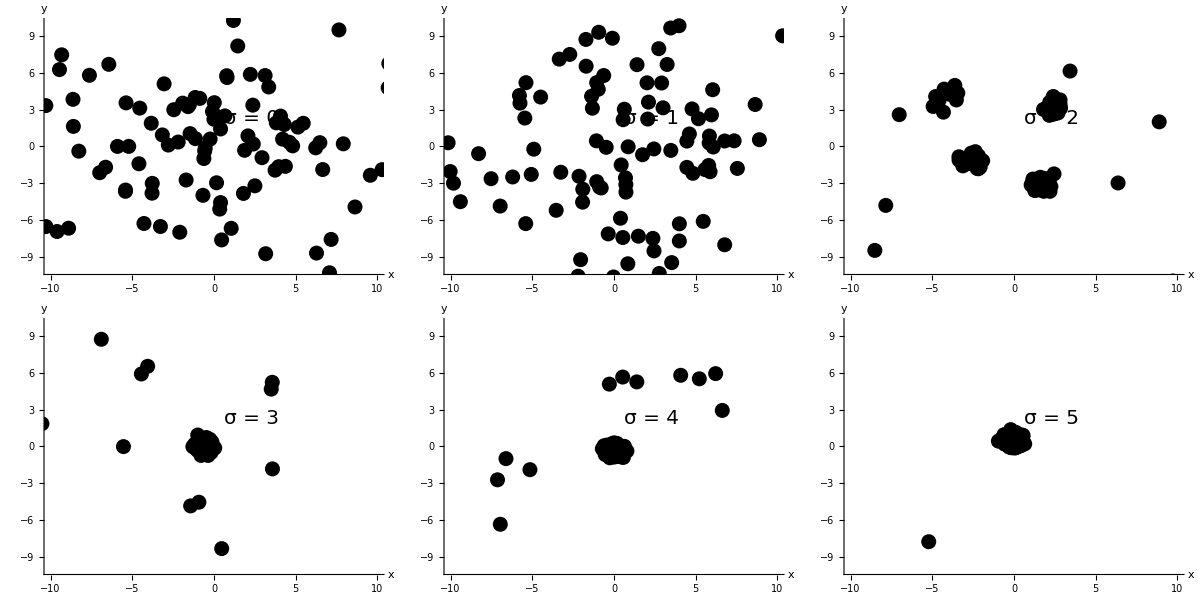

```mathematica
plotLocal[z_,L_,σ_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text[Style["σ = "<>ToString[σ],20],{2.3,2.3}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->19];
Return[p1];
];
plots=Table[plotLocal[dataZσ[[i]],10,σs[[i]]],{i,1,Length[σs]}];
p1=Grid[Partition[plots,3]]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-states-different-σ.png",p1];
```

### Vary Ω

```mathematica
plotLocal[z_,L_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text["d = 1",{2.5,2.5}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];
Return[p1];
];

run[Ω_,d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,cutoff},
{dt,T,n}={0.25,400,300};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=ω-Mean[ω];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
Return[znew];
];
```

```mathematica
Ωs=Table[Ω,{Ω,0.5,2,0.25}];
dataZd=ParallelTable[run[Ω,0,10],{Ω,Ωs}];
```

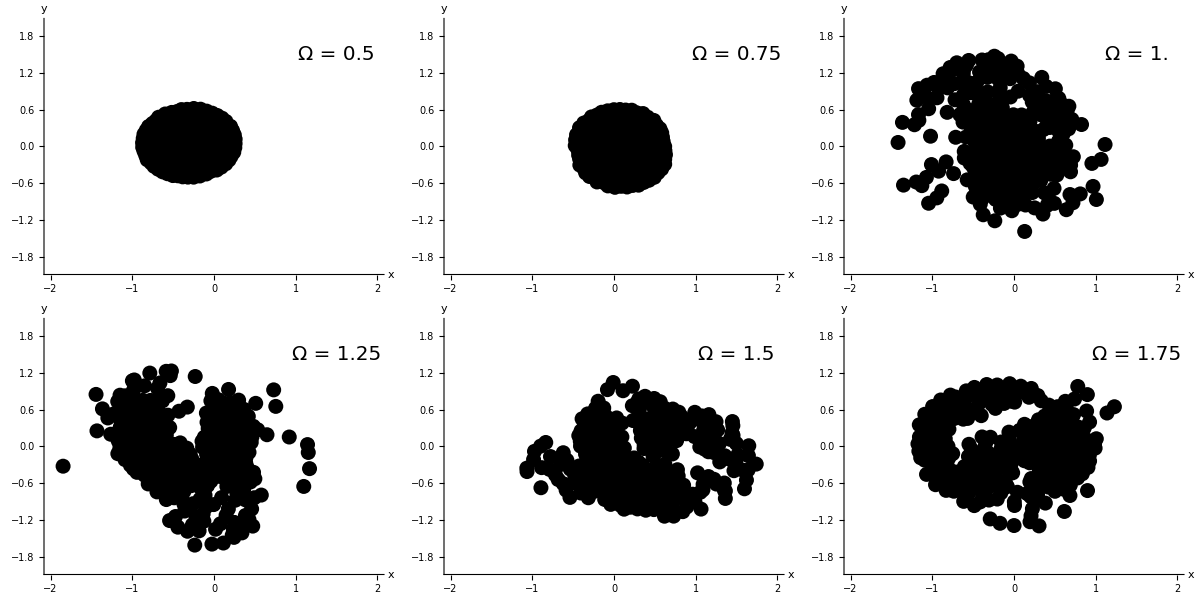

```mathematica
plotLocal[z_,L_,Ω_]:=Block[{colors,p1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},Epilog->{Text[Style["Ω = "<>ToString[Ω],20],{1.5,1.5}]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->19];
Return[p1];
];
plots=Table[plotLocal[dataZd[[i]],2,Ωs[[i]]],{i,1,Length[Ωs]}];
p1=Grid[Partition[plots,3]]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-states-different-omega.png",p1];
```

## R(d,σ)

### R(d) fixed σ

```mathematica
run[d_]:=Block[{dt,T,n,J,k,σ,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff},
{dt,T,n}={0.1,100,200};
{J,k,σ}={1,1,10};
{R,L,Ω}={1,5,0.1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75*Length[Zs]];
Return[Zs[[cutoff;;-1]]//Abs//Mean];
]
```

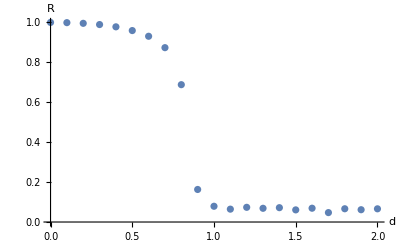

```mathematica
ds=Table[d,{d,0,2,0.1}];
dataRd=ParallelTable[{d,run[d]},{d,ds}];
ListPlot[dataRd,PlotRange->All,AxesLabel->{"d","R"},LabelStyle->15]
```

#### Make for paper

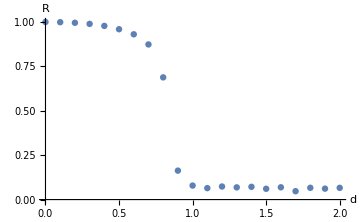

```mathematica
dataRd={{0.,0.9999999999999972},{0.1,0.9989516197408521},{0.2,0.9955658570623388},{0.30000000000000004,0.9893947188387969},{0.4,0.9779881441516557},{0.5,0.9592772833807899},{0.6000000000000001,0.9307394761237892},{0.7000000000000001,0.8736116760191279},{0.8,0.6881579511222758},{0.9,0.163038437722705},{1.,0.07893750756206516},{1.1,0.06446027658456638},{1.2000000000000002,0.07362933942572385},{1.3,0.06873554560825897},{1.4000000000000001,0.07184577164513191},{1.5,0.06080417977401676},{1.6,0.06913084284943048},{1.7000000000000002,0.04717728666285989},{1.8,0.06642618027230425},{1.9000000000000001,0.06161735499666811},{2.,0.0661506983872535}};

p1=ListPlot[dataRd,PlotRange->All,AxesLabel->{Style["d",18,Italic],Style["R",Italic,18]},LabelStyle->15,ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-kuramto-order-par-versus-d.png",p1];
```

#### Plot for different Ω

```mathematica
run[d_,Ω_]:=Block[{dt,T,n,J,k,σ,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,cutoff},
{dt,T,n}={0.25,500,300};
{J,k,σ}={1,1,10};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω-=Mean[ω];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75*Length[Zs]];
Return[Zs[[cutoff;;-1]]//Abs//Mean];
];
```

```mathematica
allData=Table[
ds=Table[d,{d,0,1.2,0.01}];
dataRd=ParallelTable[{d,run[d,Ω]},{d,ds}];
dataRd,
{Ω,0,2,0.5}
];
```

$Aborted

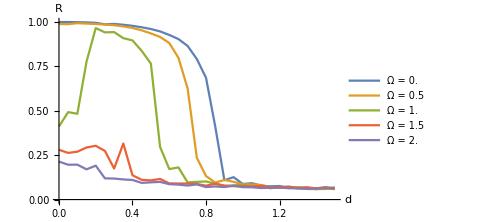

```mathematica
Ωs=Table[i,{i,0,2,0.5}];
ListPlot[allData,PlotRange->All,AxesLabel->{Style["d",17,Italic],Style["R",17,Italic]},LabelStyle->15,ImageSize->Medium,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],Joined->True]
```

```mathematica
p1=ListPlot[allData,PlotRange->All,AxesLabel->{Style["d",17,Italic],Style["R",17,Italic]},LabelStyle->15,ImageSize->Medium,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],Joined->True];
Export["figures/sync-R-d-different-omega.png",p1];
```

Look at that state. There’s an interesting effect; noise kills the drifters.

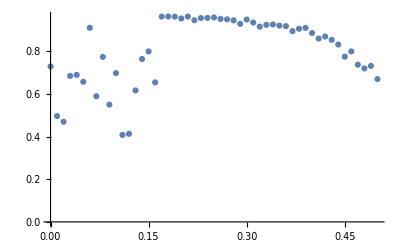

```mathematica
ds=Table[d,{d,0,0.5,0.01}];
dataRd=ParallelTable[{d,run[d,1]},{d,ds}];
ListPlot[dataRd]
```

### R(σ), fixed d

```mathematica
run[σ_]:=Block[{dt,T,n,J,k,d,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,Ω,cutoff},
{dt,T,n}={0.25,300,300};
{J,k,d}={1,1,0.5};
{R,L,Ω}={1,5,0.1};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75*Length[Zs]];
Return[Zs[[cutoff;;-1]]//Abs//Mean];
];
```

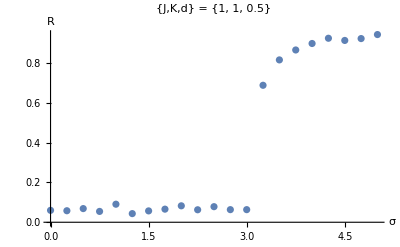

```mathematica
σs=Table[σ,{σ,0,5,0.25}];
dataRs=ParallelTable[{σ,run[σ]},{σ,σs}];
ListPlot[dataRs,PlotRange->All,AxesLabel->{"σ","R"},LabelStyle->15,PlotLabel->"{J,K,d} = "<>ToString[{1,1,0.5}]]
```

#### For paper

Need to take some averages here. But looking as expected.

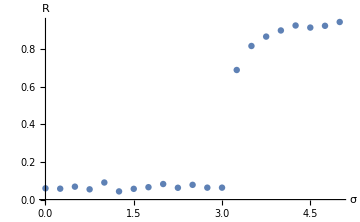

```mathematica
dataRs={{0.,0.059916716192576984},{0.25,0.05794551510273122},{0.5,0.06874541004487666},{0.75,0.05452080788234092},{1.,0.09076968437628558},{1.25,0.04345267340598254},{1.5,0.057128780112578964},{1.75,0.06590358684798839},{2.,0.08268750749105307},{2.25,0.06279708590577618},{2.5,0.0783943032859959},{2.75,0.06343597971794043},{3.,0.06343370044532314},{3.25,0.6890526002866225},{3.5,0.8167444507657776},{3.75,0.8666840415889886},{4.,0.89927647788547},{4.25,0.9256717042438497},{4.5,0.9146328032169481},{4.75,0.9240540986526694},{5.,0.9442938728633246}};

p1=ListPlot[dataRs,PlotRange->All,AxesLabel->{Style["σ",18,Italic],Style["R",Italic,18]},LabelStyle->15,ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-kuramto-order-par-versus-σ.png",p1];
```

### R(Ω), fixed d

```mathematica
run[Ω_,d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,cutoff},
{dt,T,n}={0.25,200,300};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=ω-Mean[ω];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75*Length[Zs]];
Return[Zs[[cutoff;;-1]]//Abs//Mean];
];
```

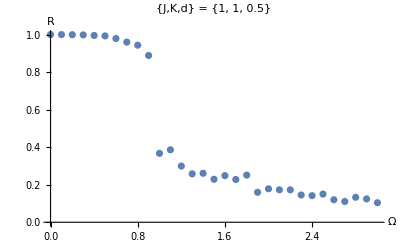

```mathematica
Ωs=Table[d,{d,0,3,0.1}];
dataRo=ParallelTable[{Ω,run[Ω,0,10]},{Ω,Ωs}];
ListPlot[dataRo,PlotRange->All,AxesLabel->{"Ω","R"},LabelStyle->15,PlotLabel->"{J,K,d} = "<>ToString[{1,1,0.5}]]
```

#### For paper

Need to take some averages here. But looking as expected.

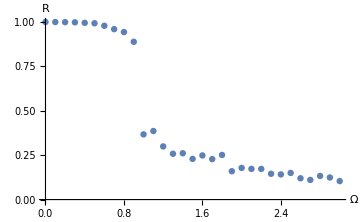

```mathematica
dataRo={{0.,1.0000000000000013},{0.1,0.9997566192374456},{0.2,0.9990859069555887},{0.30000000000000004,0.9981017209481494},{0.4,0.9953372162008969},{0.5,0.9928341228125702},{0.6000000000000001,0.9786408129937901},{0.7000000000000001,0.9597176795760219},{0.8,0.9433249914040835},{0.9,0.8885766623290058},{1.,0.36717293901875},{1.1,0.38606693009284404},{1.2000000000000002,0.29937029570268986},{1.3,0.2578854452484507},{1.4000000000000001,0.26085171797977835},{1.5,0.22910073419797475},{1.6,0.24850308991395995},{1.7000000000000002,0.2278435783176533},{1.8,0.2511630498032052},{1.9000000000000001,0.15960873499241193},{2.,0.1782809277734658},{2.1,0.17289046531032334},{2.2,0.17253200089580867},{2.3000000000000003,0.14528310569390324},{2.4000000000000004,0.14175436192462754},{2.5,0.14995665350722914},{2.6,0.11987907485473288},{2.7,0.11071999022012134},{2.8000000000000003,0.13299723682085746},{2.9000000000000004,0.12436653408563138},{3.,0.10400288437850325}};

p1=ListPlot[dataRo,PlotRange->All,AxesLabel->{Style["Ω",18,Italic],Style["R",Italic,18]},LabelStyle->15,ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-kuramto-order-par-versus-omega.png",p1];
```

```mathematica
plots
```

#### Vary d in same plot

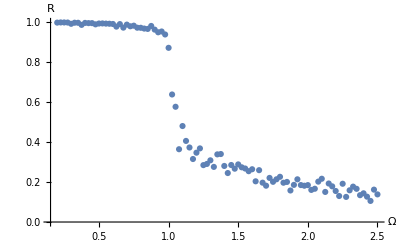

```mathematica
run[Ω_,d_,σ_]:=Block[{dt,T,n,J,k,t,NT,Z1,Z,Wp,Wm,Zs,Wps,Wms,z0,znew,R,L,ω,cutoff},
{dt,T,n}={0.25,200,200};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=ω-Mean[ω];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{Z,Wp,Wm}=findOrderPars[znew];
z0=znew;t++;AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];
];
cutoff=Round[0.75*Length[Zs]];
Return[Zs[[cutoff;;-1]]//Abs//Mean];
];

d=0.1;
Ωs=Table[Ω,{Ω,0.2,2.5,0.025}];
dataRo=ParallelTable[{Ω,run[Ω,d,10]},{Ω,Ωs}];
ListPlot[dataRo,PlotRange->All,AxesLabel->{Style["Ω",17,Italic],Style["R",17,Italic]},LabelStyle->15]
```

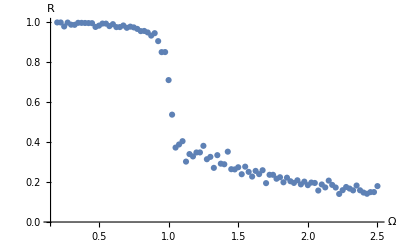

```mathematica
d=0.05;
Ωs=Table[Ω,{Ω,0.2,2.5,0.025}];
dataRo=ParallelTable[{Ω,run[Ω,d,10]},{Ω,Ωs}];
ListPlot[dataRo,PlotRange->All,AxesLabel->{Style["Ω",17,Italic],Style["R",17,Italic]},LabelStyle->15]
```

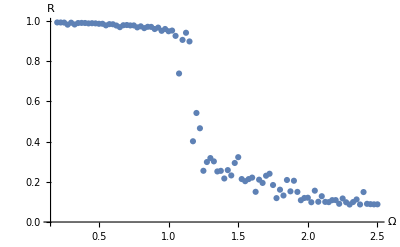

```mathematica
d=0.2;
Ωs=Table[Ω,{Ω,0.2,2.5,0.025}];
dataRo=ParallelTable[{Ω,run[Ω,d,10]},{Ω,Ωs}];
ListPlot[dataRo,PlotRange->All,AxesLabel->{Style["Ω",17,Italic],Style["R",17,Italic]},LabelStyle->15]
```

Not quite clear.

### C(v,v)(t)

$Aborted

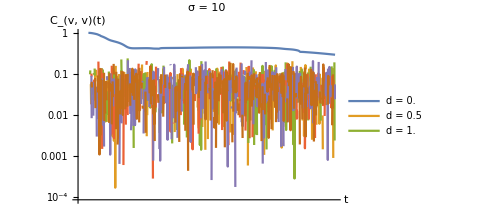
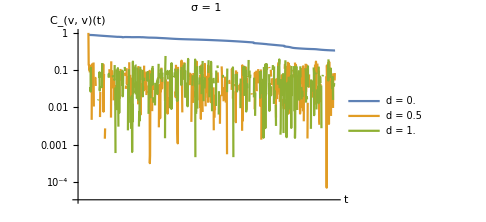
-Graphics- | -Graphics-

```mathematica
run[d_,σ_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,Ω},
{dt,T,n}={0.25,500,100};
{J,k}={1,1};
{R,L,Ω}={1,5,0.1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,theta]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
c=findVelAutoCorr[xs,ys,dt,NT];
Return[c]
]

σ=10;
ds=Table[d,{d,0,1,0.5}];
dataCveld1=ParallelTable[run[d,σ],{d,ds}];
p1=ListLogLogPlot[dataCveld1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["d = "<>ToString[d],{d,ds}],PlotLabel->"σ = "<>ToString[σ],ImageSize->Medium];

σ=1;
ds=Table[d,{d,0,1,0.5}];
dataCveld2=ParallelTable[run[d,σ],{d,ds}];
p2=ListLogLogPlot[dataCveld2,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["d = "<>ToString[d],{d,ds}],PlotLabel->"σ = "<>ToString[σ],ImageSize->Medium];

Grid[{{p1,p2}}]
```

I guess it makes sense, the motion is pure white noise, so uncorrelated for even small d. Hmm.

### C(v,v)(σ) for fixed d

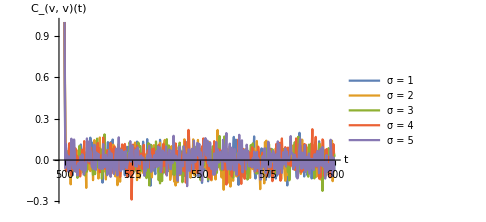

```mathematica
run[d_,σ_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,Ω},
{dt,T,n}={0.25,200,100};
{J,k}={1,1};
{R,L,Ω}={1,5,0.1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,theta]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
c=findVelAutoCorr[xs,ys,dt,NT];
Return[c]
]

d=0;
σs=Table[σ,{σ,1,5,1}];
dataCvels1=ParallelTable[run[d,σ],{d,σs}];
p2=ListPlot[dataCvels1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["σ = "<>ToString[σ],{σ,σs}],ImageSize->Medium,PlotRange->{Automatic,1.1}]
```

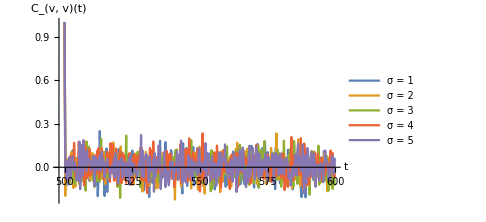

```mathematica
d=0.25;
σs=Table[σ,{σ,1,5,1}];
dataCvels1=ParallelTable[run[d,σ],{d,σs}];
p2=ListPlot[dataCvels1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["σ = "<>ToString[σ],{σ,σs}],ImageSize->Medium,PlotRange->{Automatic,1.1}]
```

## Correlations

### Methods

```mathematica
findRijNij[xs_,ys_,θs_,t_,n_]:=Block[{dataRijNij,rij,nij,i,j},
dataRijNij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
AppendTo[dataRijNij,{rij,nij}]
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
];

clean[data_]:=Block[{cleanData,element,condition},
cleanData={};
For[i=1,i≤Length[data],i++,
element=data[[i]];
condition=NumberQ[element[[1]]]&&NumberQ[element[[2]]];
If[condition,AppendTo[cleanData,element]]
];
Return[cleanData]
]

findCthetathetaR[xs_,ys_,θs_,t_,n_]:=Block[{data,dr,rmax,binnedData,meanBinnedData,RijNijpairs},
RijNijpairs=findRijNij[xs,ys,θs,t,n]; (**)
dr=0.1;
rmax=Ceiling[Max[RijNijpairs[[All,1]]]]+1;
binnedData=BinLists[RijNijpairs,{0,rmax,dr},{-1,1,2}];
meanBinnedData=Table[{binnedData[[i,1]][[All,1]]//Mean,binnedData[[i,1]][[All,2]]//Mean},{i,1,Length[binnedData]}];
(*meanBinnedData=clean[meanBinnedData];*)
Return[{RijNijpairs,meanBinnedData}]
];

run1[σ_,d_]:=Block[{dt,T,n,J,k,R,L,ω,z0,znew,t,NT,xs,ys,θs,x,y,θ},
{dt,T,n}={0.25,200,300};
{J,k}={1,1};
{R,L}={1,5};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];{x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
];
Return[{znew,xs,ys,θs}];
];
```

### C(θ,θ)(r) -- for different d

```mathematica
allData={};
```

#### d = 0

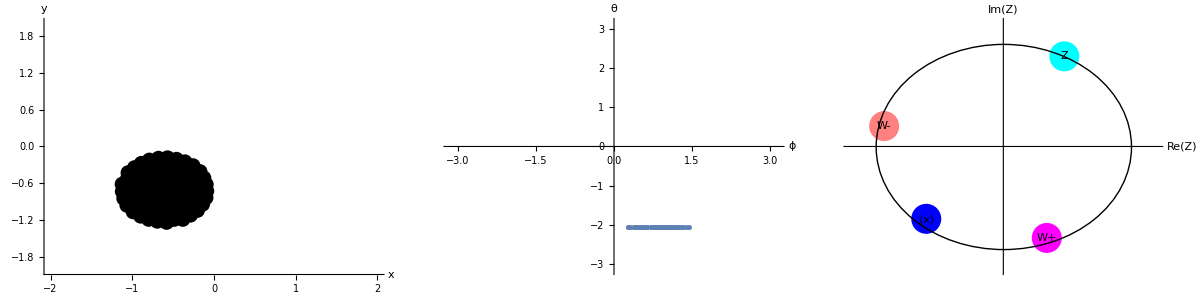

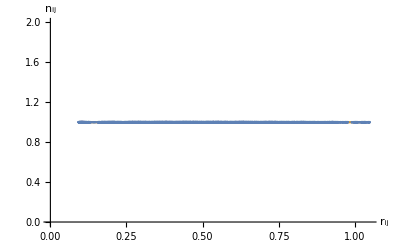

```mathematica
{σ,d}={10,0};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,2]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,datadzero}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,datadzero},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

#### d = 0.2

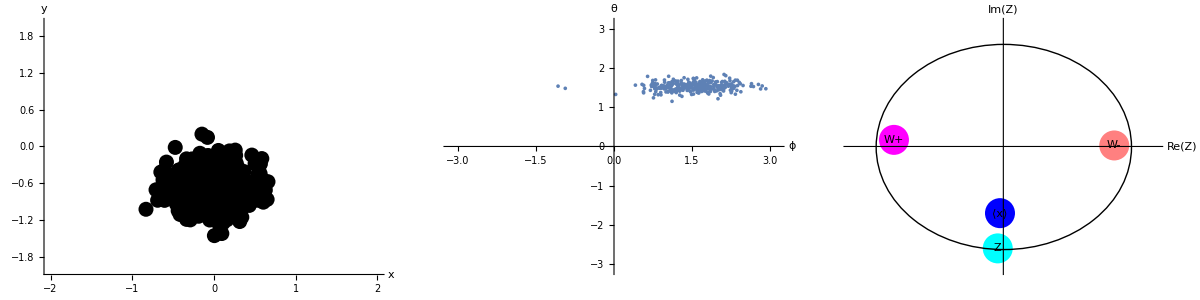

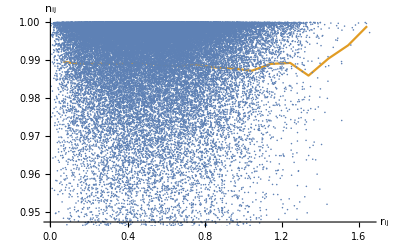

```mathematica
{σ,d}={10,0.2};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,2]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,datadtwo}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,datadtwo},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

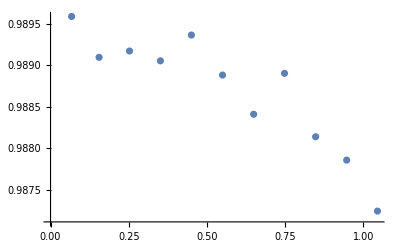

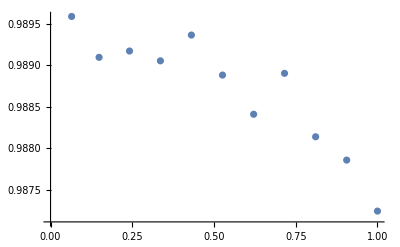

```mathematica
datadtwoClean=clean[datadtwo[[1;;-20]]];
ListPlot[datadtwoClean]
datadtwoClean={datadtwoClean[[All,1]]/Max[datadtwoClean[[All,1]]],datadtwoClean[[All,2]]}ᵀ;
ListPlot[datadtwoClean]
```

#### d = 0.4

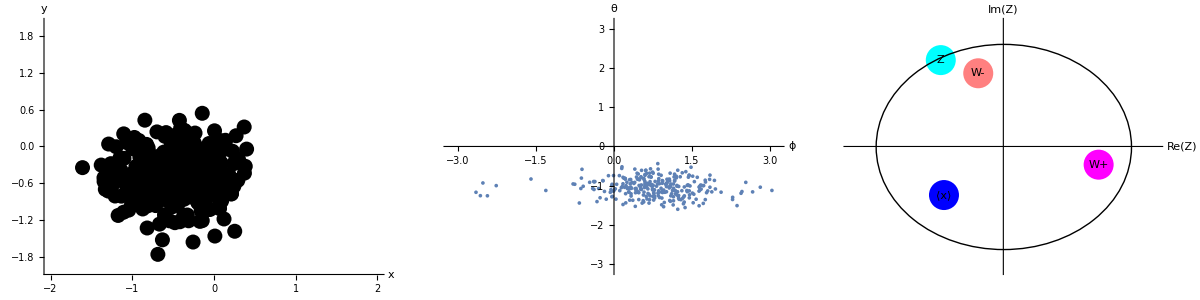

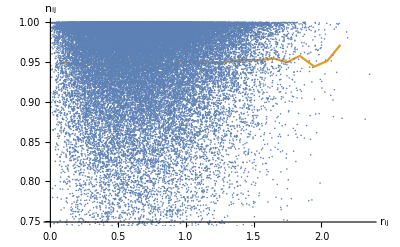

```mathematica
{σ,d}={10,0.4};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,2]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,datadfour}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,datadfour},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

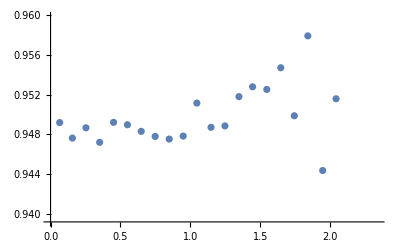

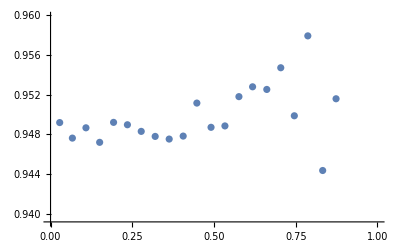

```mathematica
datadfourClean=clean[datadfour[[1;;-1]]];
ListPlot[datadfourClean]
datadfourClean={datadfourClean[[All,1]]/Max[datadfourClean[[All,1]]],datadfourClean[[All,2]]}ᵀ;
ListPlot[datadfourClean]
```

```mathematica
datadfourClean
```

{{0.0655192/Max[2.3391,Mean[{}]],0.949193},{0.156278/Max[2.3391,Mean[{}]],0.947626},{0.253366/Max[2.3391,Mean[{}]],0.948664},{0.351434/Max[2.3391,Mean[{}]],0.947199},{0.450974/Max[2.3391,Mean[{}]],0.949213},{0.550079/Max[2.3391,Mean[{}]],0.948972},{0.648865/Max[2.3391,Mean[{}]],0.948304},{0.748704/Max[2.3391,Mean[{}]],0.947796},{0.848909/Max[2.3391,Mean[{}]],0.947529},{0.949061/Max[2.3391,Mean[{}]],0.94783},{1.04692/Max[2.3391,Mean[{}]],0.951159},{1.14839/Max[2.3391,Mean[{}]],0.948714},{1.24779/Max[2.3391,Mean[{}]],0.948854},{1.34793/Max[2.3391,Mean[{}]],0.951809},{1.44563/Max[2.3391,Mean[{}]],0.952801},{1.54727/Max[2.3391,Mean[{}]],0.952534},{1.64724/Max[2.3391,Mean[{}]],0.954722},{1.74431/Max[2.3391,Mean[{}]],0.949877},{1.84084/Max[2.3391,Mean[{}]],0.957938},{1.94714/Max[2.3391,Mean[{}]],0.944357},{2.04286/Max[2.3391,Mean[{}]],0.951594},{2.13973/Max[2.3391,Mean[{}]],0.971834},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{2.3391/Max[2.3391,Mean[{}]],0.906572},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]},{Mean[{}]/Max[2.3391,Mean[{}]],Mean[{}]}}

#### d = 0.6

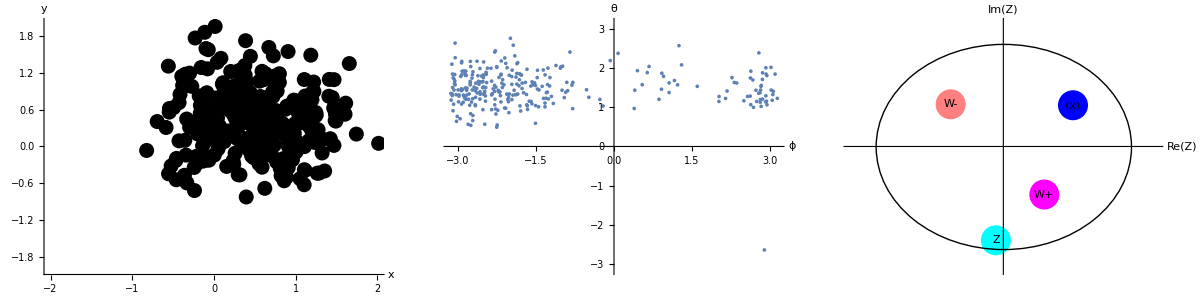

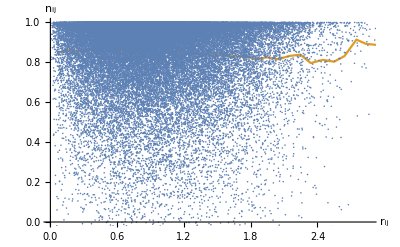

```mathematica
{σ,d}={10,0.6};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,2]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,datadsix}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,datadsix},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

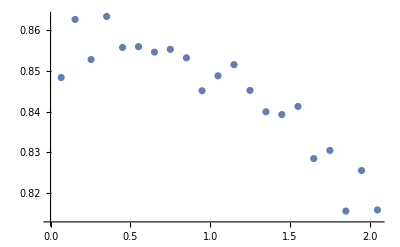

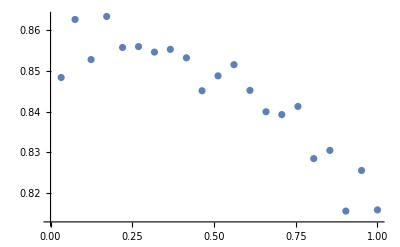

```mathematica
datadsixClean=datadsix[[1;;-150]];
ListPlot[datadsixClean]
datadsixClean={datadsixClean[[All,1]]/Max[datadsixClean[[All,1]]],datadsixClean[[All,2]]}ᵀ;
ListPlot[datadsixClean]
```

#### d = 0.8

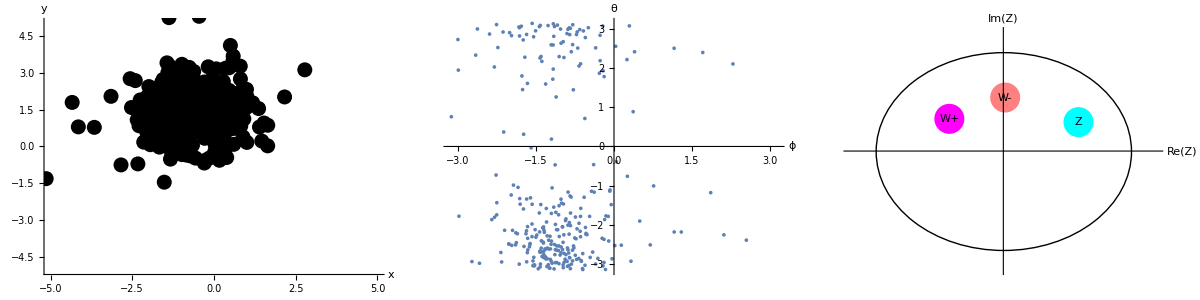

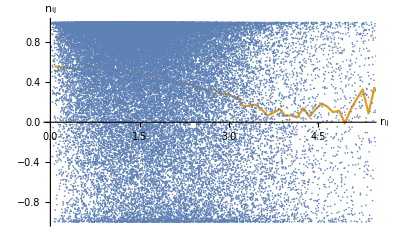

```mathematica
{σ,d}={10,0.8};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,5]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,datadeight}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,datadeight},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

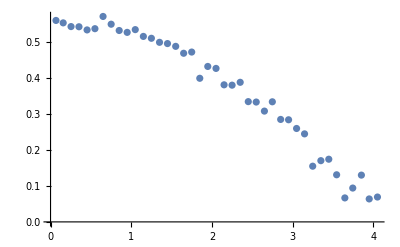

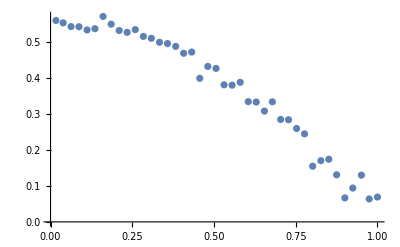

```mathematica
datadeightClean=datadeight[[1;;-70]];
ListPlot[datadeightClean]
datadeightClean={datadeightClean[[All,1]]/Max[datadeightClean[[All,1]]],datadeightClean[[All,2]]}ᵀ;
ListPlot[datadeightClean]
```

#### d = 1

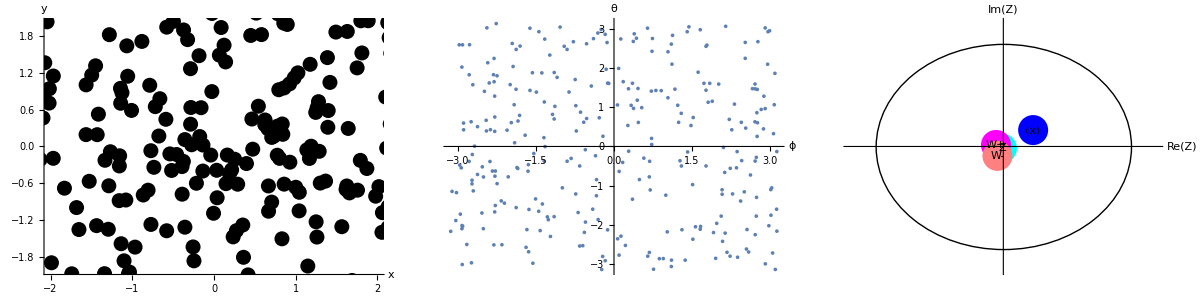

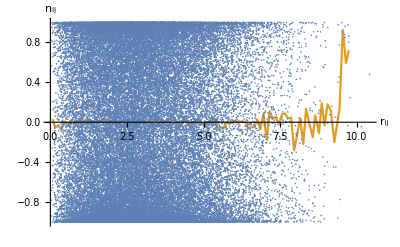

```mathematica
{σ,d}={10,1};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,5]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,datadone}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,datadone},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

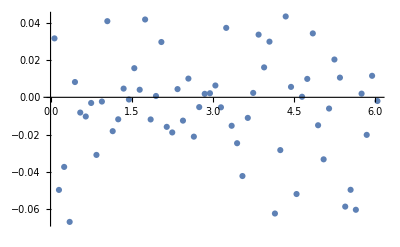

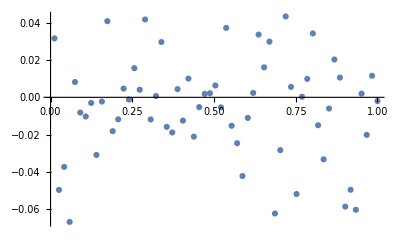

```mathematica
datadoneClean=datadone[[1;;-60]];
ListPlot[datadoneClean]
datadoneClean={datadoneClean[[All,1]]/Max[datadoneClean[[All,1]]],datadoneClean[[All,2]]}ᵀ;
ListPlot[datadoneClean]
```

### Plot all

#### Data -- collected from above

```mathematica
allData={{{0.09694726589329594,0.9999999999999999},{0.15445615510141547,0.9999999999999999},{0.2572804605878365,0.9999999999999999},{0.35564109592654564,0.9999999999999999},{0.4520970470803563,0.9999999999999999},{0.5472031949058634,0.9999999999999999},{0.6441166191784232,0.9999999999999999},{0.7425092638453159,0.9999999999999999},{0.8387824754720182,0.9999999999999999},{0.931114771435805,0.9999999999999999},{1.0245296426591812,0.9999999999999999},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]}},{{0.06449862722082637,0.989585843280111},{0.14845091127140916,0.9890942841142182},{0.24156262551831317,0.9891702165100682},{0.3360990255916207,0.9890520682619315},{0.4308315948986537,0.9893623859479157},{0.5260710933543131,0.9888808786882735},{0.6212841878354414,0.9884093578300639},{0.7157115585235816,0.9889016864076076},{0.8108587633877081,0.9881387378438325},{0.9058557030174839,0.9878580215047983},{0.9999999999999999,0.9872447792087002}},{{0.028010388400925974,0.9491930727405948},{0.06681120796903824,0.9476259683105422},{0.10831766388234068,0.9486644070706738},{0.15024306283576155,0.9471988305597393},{0.19279773282714746,0.9492125895897461},{0.23516648846871918,0.9489722216779675},{0.2773989525700969,0.9483041232683129},{0.3200816118072851,0.9477961756591288},{0.36292044601341533,0.9475289571500966},{0.40573683023335283,0.9478297258679036},{0.44757265824270714,0.9511590122250909},{0.49095208959150416,0.948714114984157},{0.5334494859122283,0.9488540073232169},{0.5762602074500567,0.951808626997546},{0.6180268802711777,0.9528006671878159},{0.6614790623439148,0.9525340412574043},{0.7042192340301509,0.9547219155339883},{0.7457148403679943,0.9498774768854078},{0.7869841432302043,0.9579382846642487},{0.8324306426986282,0.9443570985341683},{0.8733491747863213,0.9515941338862003},{0.9147649869989402,0.9718336115885616},{1.,0.9065718912258913}},{{0.03250436851390653,0.848401823118161},{0.07500870277650305,0.8627246857941463},{0.12398280210334552,0.8528254095137451},{0.1716813075271394,0.8634606149809211},{0.22035375137849253,0.8558049381919959},{0.2690826992862007,0.8560216210461592},{0.3178904130703749,0.8546649237799524},{0.36643429974392383,0.8553440187891347},{0.4155944825263549,0.8532537030521709},{0.46340934594595357,0.8451273169340745},{0.5123013765852343,0.8488040729120316},{0.561166074640169,0.8515627116717717},{0.6100196322370377,0.8452159745156151},{0.6590011895589128,0.8399411367660332},{0.707336306964019,0.8392490097895415},{0.7568561819271497,0.8412598772567608},{0.8051064693713396,0.8283867093452296},{0.8544566440518141,0.8304039835783295},{0.9032268156007546,0.8154314696850223},{0.9513630942858853,0.8254547105381882},{1.,0.8157205006824558}},{{0.016677452922499066,0.5607865413268507},{0.0386875257518073,0.5540077123112931},{0.0627060270073484,0.5437104775373144},{0.08697721470461169,0.5431860154136335},{0.11176595791833902,0.5343854047029022},{0.13577938444087675,0.5378273159464576},{0.1606070051522044,0.5718634660815941},{0.18542710318091082,0.5502851645092773},{0.21000936896636624,0.5327774939124826},{0.23443183423731212,0.5275704329686786},{0.2591438348750355,0.5352086099561907},{0.2839350859758361,0.5163210956616343},{0.3084808254481306,0.5111181914864561},{0.3333618892127282,0.4998782480769974},{0.35770908537119595,0.4963908033115877},{0.3828057594915502,0.48865967945514055},{0.4071719230323701,0.46940640375019466},{0.43177765249117034,0.47279556271511697},{0.45649588677029473,0.39976117844721737},{0.4809582992482594,0.4326985675340156},{0.5061684845532326,0.42723826503808915},{0.5308101230794947,0.3815821258418416},{0.5553087958289248,0.38061059982714784},{0.5801268085701123,0.3885647310450686},{0.6048360856028626,0.33478068627933205},{0.6291389485786951,0.33362562250202166},{0.6541905589883307,0.3084269918841128},{0.6784361121628036,0.3343268723582717},{0.7039154001041091,0.2852146534901642},{0.7281072410394563,0.28427640102804147},{0.7525806684593573,0.26004244539668986},{0.7769810113040069,0.24504174869153617},{0.8019051488053042,0.155055492445218},{0.8268776449436548,0.17044862218856469},{0.8511006729075674,0.17448047848579062},{0.8750928980264072,0.13115593984914445},{0.9002500071160493,0.06674454410059487},{0.9244322922285579,0.09421838278659694},{0.9508602549668297,0.13020665828829514},{0.9747509178882153,0.06391990290435326},{1.,0.06921685997547286}},{{0.012058203792345974,0.031583334687526894},{0.025752282486657726,-0.04961348231771582},{0.041670251005312124,-0.03729087637805164},{0.05849181147220769,-0.06675107846435345},{0.07470112052128555,0.008194217740125067},{0.09088185312525367,-0.008169539985546134},{0.10775258005994327,-0.010268355451201484},{0.12423289156158672,-0.0030273765979553476},{0.1404255859416144,-0.030863004285953136},{0.15708911744730694,-0.0022650170206357464},{0.17373813227797139,0.04080663944939213},{0.19014877916246964,-0.018136944935988913},{0.20702087507751596,-0.011773714755429012},{0.2235238943814644,0.004671117832821124},{0.23978455165222354,-0.0011678441534573925},{0.25621459621959763,0.01561331311147341},{0.27272920159890035,0.004062875018430816},{0.2892724616943944,0.04170658966023899},{0.30621750280225307,-0.011854009347645167},{0.32256261765289523,0.0007133449374183659},{0.3390331169412844,0.029634209408915625},{0.3554581801970569,-0.01582192403543533},{0.372288234867432,-0.018819994671764494},{0.3884599632458589,0.0044071026970618635},{0.4050691791270192,-0.01248707772922201},{0.4216929015485267,0.010033637675967563},{0.43839581387179943,-0.021071366882504366},{0.4547713442633561,-0.005243911235038842},{0.4716122895521768,0.0018676115454123747},{0.4875690410764173,0.0021819621818557735},{0.5042370169305624,0.006342735869671314},{0.5212379632342589,-0.005357317576451257},{0.5373617301001246,0.037211197731257695},{0.5539829401285402,-0.015244853538611096},{0.5706538325050208,-0.024593638636487558},{0.5870333290508685,-0.04217228306824208},{0.603367220796898,-0.011025762438147367},{0.6198697108266852,0.00235896000703639},{0.6363994547238615,0.03359255484617943},{0.6532883938681004,0.016046530044666076},{0.6696689717387188,0.029832767932055627},{0.6863734395915718,-0.06225516579386288},{0.7027861456103692,-0.0282813210411949},{0.7193298321108217,0.04332837762562723},{0.7355772842657713,0.005589225655743574},{0.7524816141386239,-0.05181776745016534},{0.7693240709194974,0.00030497218585562216},{0.7852803358832334,0.009869839143224849},{0.8022501159740686,0.034245362177832556},{0.8183756794287732,-0.014966844446746848},{0.8353381047672145,-0.03323054173908767},{0.8519546145607566,-0.006009402583810984},{0.8683709352119611,0.02026305221237772},{0.8852292317935276,0.010556212153567711},{0.90137541714973,-0.0585519472120917},{0.9178171098653649,-0.04955608624722605},{0.933935600517518,-0.06024906609799835},{0.9513990280681567,0.0019748340647157483},{0.9671296282194437,-0.020120074923522788},{0.9835736537008128,0.011529982163797324},{1.,-0.0019699217083497156}}};
```

#### Plot: (J,K,σ) = (1,1,10)

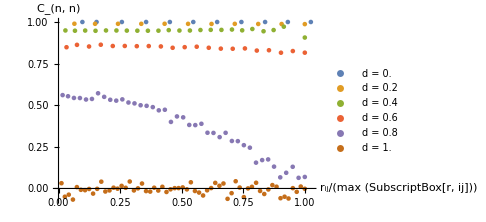

```mathematica
p1=ListPlot[allData,AxesLabel->{Style["r_ij/(max (SubscriptBox[r, ij]))",17],Style["C_(n, n)",18]},PlotLegends->{Table["d = "<>ToString[d],{d,0,1,0.2}]},ImageSize->Medium,LabelStyle->14]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-phase-rij.png",p1]
```

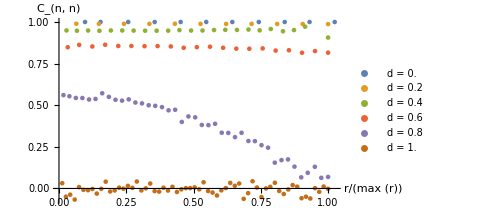

figures/sync-corr-phase-rij.png

```mathematica
p1=ListPlot[allData,AxesLabel->{Style["r/(max (r))",17],Style["C_(n, n)",18]},PlotLegends->{Table["d = "<>ToString[d],{d,0,1,0.2}]},ImageSize->Medium,LabelStyle->14]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-phase-rij.png",p1]
```

### C(v,v)(t)

#### Identical

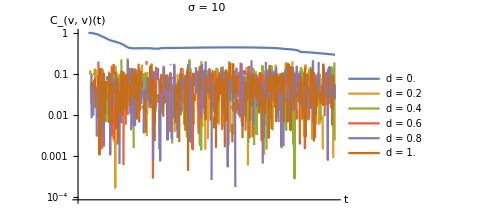
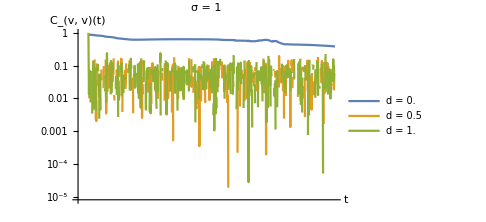
-Graphics- | -Graphics-

```mathematica
run[d_,σ_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,Ω},
{dt,T,n}={0.25,500,100};
{J,k}={1,1};
{R,L,Ω}={1,5,0.1};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
ω=Table[RandomChoice[{-Ω,Ω}],n];
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,theta]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
c=findVelAutoCorr[xs,ys,dt,NT];
Return[c]
]

σ=10;
ds=ParallelTable[d,{d,0,1,0.2}];
dataCveld1=ParallelTable[run[d,σ],{d,ds}];
p1=ListLogLogPlot[dataCveld1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["d = "<>ToString[d],{d,ds}],PlotLabel->"σ = "<>ToString[σ],ImageSize->Medium];

Grid[{{p1,p2}}]
```

I guess it makes sense, the motion is pure white noise, so uncorrelated for even small d. Hmm.

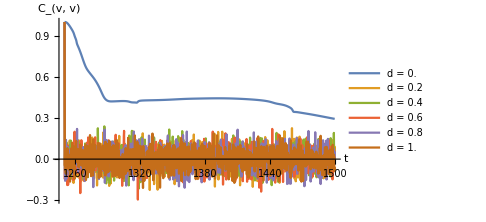

figures/sync-corr-vel-vel.png

```mathematica
p1=ListPlot[dataCveld1,PlotRange->All,Joined->True,AxesLabel->{Style["t",22,Italic],Style["C_(v, v)",17]},LabelStyle->15,PlotLegends->Table["d = "<>ToString[d],{d,ds}],ImageSize->Medium]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-vel-vel.png",p1]
```

#### Non identical

```mathematica
run[d_,σ_,Ω_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,ts},
{dt,T,n}={0.25,1000,200};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
ts={};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;AppendTo[ts,t*dt];
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
cutoff=Round[0.5*NT];
c=findVelAutoCorr[xs,ys,dt,NT];
Return[c]
];

findVelAutoCorr[xs_,ys_,dt_,NT_]:=Block[{vx,vy,v,tcutoff,c},
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
tcutoff=Round[0.1*NT];
c=Table[
{t dt,Sum[Normalize[v[[i,tcutoff]]].Normalize[v[[i,t]]],{i,1,n}]/n},
{t,tcutoff,NT-1}
];
Return[c]
];
```

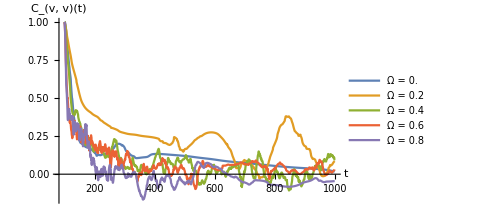

```mathematica
{d,σ}={0,10};
Ωs=Table[Ω,{Ω,0,0.8,0.2}];
data=ParallelTable[run[d,σ,Ω],{Ω,Ωs}];
p1=ListPlot[data,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium]
```

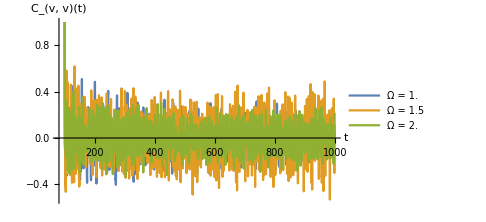

```mathematica
{d,σ}={0,10};
Ωs=Table[Ω,{Ω,1,2,0.5}];
data2=ParallelTable[run[d,σ,Ω],{Ω,Ωs}];
p2=ListPlot[data2,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium]
```

```mathematica
p3=Grid[{{p1,p2}}]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-vel-auto-omega.png",p3]
```

-Graphics- | -Graphics-

figures/sync-corr-vel-auto-omega.png

#### Ensemble

```mathematica
run[d_,σ_,Ω_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,ts},
{dt,T,n}={0.25,1000,100};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
ts={};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;AppendTo[ts,t*dt];
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
cutoff=Round[0.5*NT];
c=findVelAutoCorr[xs,ys,dt,NT];
Return[c]
];

findVelAutoCorr[xs_,ys_,dt_,NT_]:=Block[{vx,vy,v,tcutoff,c},
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
tcutoff=Round[0.1*NT];
c=Table[
{t dt,Sum[Normalize[v[[i,tcutoff]]].Normalize[v[[i,t]]],{i,1,n}]/n},
{t,tcutoff,NT-1}
];
Return[c]
];

runEnsemble[d_,σ_,Ω_,ntrial_]:=Block[{cs,cmean},
cs=Table[run[d,σ,Ω],{i,1,ntrials}];
cmean=Total[cs]/Length[cs];
Return[cmean]
]
```

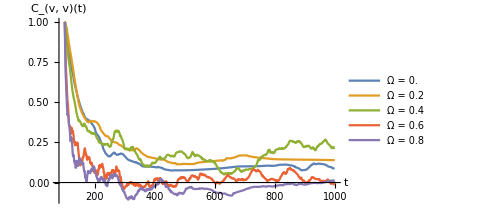

```mathematica
{d,σ,ntrial}={0,10,5};
Ωs=Table[Ω,{Ω,0,0.8,0.2}];
data1=ParallelTable[runEnsemble[d,σ,Ω,ntrial],{Ω,Ωs}];
p1=ListPlot[data1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium]
```

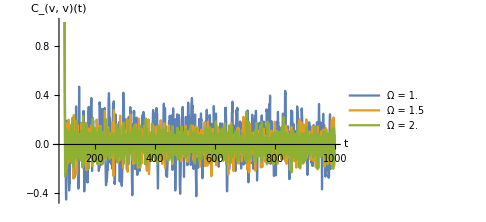

```mathematica
{d,σ,ntrial}={0,10,5};
Ωs=Table[Ω,{Ω,1,2,0.5}];
data2=ParallelTable[runEnsemble[d,σ,Ω,ntrial],{Ω,Ωs}];
p2=ListPlot[data2,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium]
```

```mathematica
p3=Grid[{{p1,p2}}]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-vel-auto-omega.png",p3]
```

-Graphics- | -Graphics-

figures/sync-corr-vel-auto-omega.png

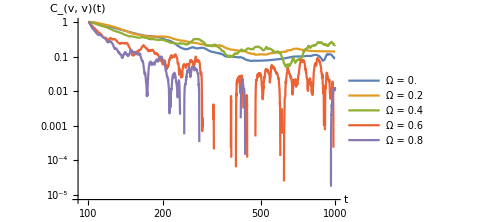
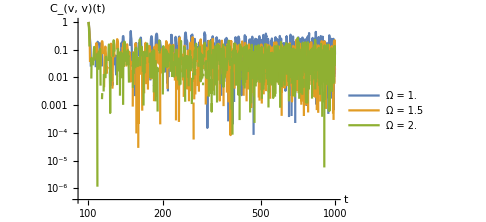
-Graphics- | -Graphics-

figures/sync-corr-vel-auto-omega.png

```mathematica
Ωs=Table[Ω,{Ω,0,0.8,0.2}];
p1=ListLogLogPlot[data1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium];
Ωs=Table[Ω,{Ω,1,2,0.5}];
p2=ListLogLogPlot[data2,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium];
p3=Grid[{{p1,p2}}]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-vel-auto-omega.png",p3]
```

#### Turn on d?

```mathematica
run[d_,σ_,Ω_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,ts},
{dt,T,n}={0.25,100,100};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
ts={};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;AppendTo[ts,t*dt];
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
cutoff=Round[0.5*NT];
c=findVelAutoCorr[xs,ys,dt,NT];
Return[c]
];

findVelAutoCorr[xs_,ys_,dt_,NT_]:=Block[{vx,vy,v,tcutoff,c},
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
tcutoff=Round[0.1*NT];
c=Table[
{t dt,Sum[Normalize[v[[i,tcutoff]]].Normalize[v[[i,t]]],{i,1,n}]/n},
{t,tcutoff,NT-1}
];
Return[c]
];
```

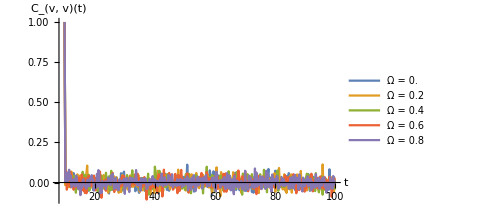

```mathematica
{d,σ,ntrial}={0.2,10,5};
Ωs=Table[Ω,{Ω,0,0.8,0.2}];
data1=ParallelTable[runEnsemble[d,σ,Ω,ntrial],{Ω,Ωs}];
p1=ListPlot[data1,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium]
```

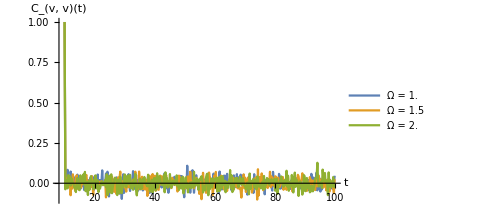

```mathematica
{d,σ,ntrial}={0.2,10,5};
Ωs=Table[Ω,{Ω,1,2,0.5}];
data2=ParallelTable[runEnsemble[d,σ,Ω,ntrial],{Ω,Ωs}];
p2=ListPlot[data2,PlotRange->All,Joined->True,AxesLabel->{"t","C_(v, v)(t)"},LabelStyle->15,PlotLegends->Table["Ω = "<>ToString[Ω],{Ω,Ωs}],ImageSize->Medium]
```

### g(r_ij)

```mathematica
findRijNijQuick=Compile[{{xs,_Real,2},{ys,_Real,2},{θs,_Real,2},{t,_Integer},{n,_Integer}},
Module[{i,j,k,rij,nij,dataRijNij},
dataRijNij=ConstantArray[0.0,{Round[n(n-1)/2],2}];
k=1;
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
dataRijNij[[k]][[1]]=rij;
dataRijNij[[k]][[2]]=nij;
k+=1
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
]
];

findRijNij[xs_,ys_,θs_,t_,n_]:=Block[{dataRijNij,rij,nij,i,j},
dataRijNij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
AppendTo[dataRijNij,{rij,nij}]
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
];
```

```mathematica
{x,y,θ}=znew;
```

```mathematica
{dt,T,n}={0.25,100,100};
{J,k,σ}={1,1,5};
{R,L,d}={1,5,0};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
plotResults[znew,5]
```

Set::shape: Lists {x,y,θ} and euler[{{-2.0242,2.30132,-2.4357,-4.54462,2.73248,0.819347,0.521686,-4.03787,3.83174,2.88788,«90»},{0.777526,3.46373,-1.38576,2.96951,-4.56184,2.99072,0.0581138,-4.29533,2.11689,3.80565,«90»},{2.70004,2.21113,-0.973651,0.116886,0.109963,-0.253238,-1.93198,-2.71579,-1.11136,2.46624,«90»}},rhs,0.25,1,1,5,{0,0,0,0,0,0,0,0,0,0,«90»},0] are not the same shape.

Set::shape: Lists {x,y,θ} and euler[euler[{{-2.0242,2.30132,-2.4357,-4.54462,2.73248,0.819347,0.521686,-4.03787,3.83174,2.88788,«90»},{0.777526,3.46373,-1.38576,2.96951,-4.56184,2.99072,0.0581138,-4.29533,2.11689,3.80565,«90»},{2.70004,2.21113,-0.973651,0.116886,0.109963,-0.253238,-1.93198,-2.71579,-1.11136,2.46624,«90»}},rhs,0.25,1,1,5,{0,0,0,0,0,0,0,0,0,0,«90»},0],rhs,0.25,1,1,5,{0,0,0,0,0,0,0,0,0,0,«90»},0] are not the same shape.

Set::shape: Lists {x,y,θ} and euler[euler[euler[{{-2.0242,2.30132,-2.4357,-4.54462,2.73248,0.819347,0.521686,-4.03787,3.83174,2.88788,«90»},{0.777526,3.46373,-1.38576,2.96951,-4.56184,2.99072,0.0581138,-4.29533,2.11689,3.80565,«90»},{2.70004,2.21113,-0.973651,0.116886,0.109963,-0.253238,-1.93198,-2.71579,-1.11136,2.46624,«90»}},rhs,0.25,1,1,5,{0,0,0,0,0,0,0,0,0,0,«90»},0],rhs,0.25,1,1,5,{0,0,0,0,0,0,0,0,0,0,«90»},0],rhs,«5»,0] are not the same shape.

General::stop: Further output of Set::shape will be suppressed during this calculation.

plotResults[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[euler[1],6,0],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],7],5]
 |  |  |  |

$Aborted

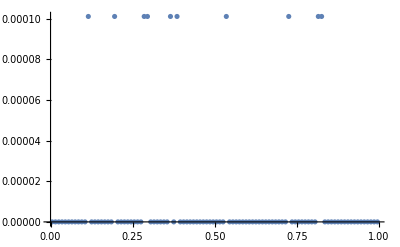

```mathematica
t=-1;
rijs=findRijNij[xs,ys,θs,t,n][[All,1]];
{min,max,dr}={0,1,0.01};
r=Table[i,{i,min,max,dr}];
r=Table[(r[[i]]+r[[i+1]])/2,{i,1,Length[r]-1}];
binnedData=BinLists[rijs,{min,max,dr}];
g=N[Table[Length[binnedData[[i]]],{i,1,Length[binnedData]}]/(n(n-1))];
ListPlot[{r,g}ᵀ,PlotRange->All]
```

```mathematica
Clear[findRijNij]
```

```mathematica
findRijNij[xs_,ys_,θs_,t_,n_]:=Block[{dataRijNij,rij,nij,i,j},
dataRijNij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
AppendTo[dataRijNij,{rij,nij}]
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
];
```

### C(θ,θ)(r) -- for different d

```mathematica
run[d_,σ_,Ω_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,ts},
{dt,T,n}={0.25,100,10};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
ts={};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;AppendTo[ts,t*dt];
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
Return[{znew,xs,ys,θs}]
];

run1[d_,σ_,Ω_]:=Block[{dt,T,n,v0,k,R,L,ω,z0,znew,t,NT,Zs,xs,ys,thetas,x,y,theta,J,Wps,Wms,cutoff,Wm,Wp,Z,θ,θs,c,ts,cr,RijNijpairs},
{dt,T,n}={0.25,100,100};
{J,k}={1,1};
{R,L}={1,5};
ω=RandomVariate[UniformDistribution[{-Ω,Ω}],n];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{Zs,Wps,Wms}={{},{},{}};
{xs,ys,θs}={{},{},{}};
ts={};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];
{x,y,θ}=znew;AppendTo[ts,t*dt];
(*{Z,Wp,Wm}=findOrderPars[znew];*)
z0=znew;t++;
AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ]
(*AppendTo[Zs,Z];AppendTo[Wps,Wp];AppendTo[Wms,Wm];*)
];
{RijNijpairs,cr}=findCthetathetaR[xs,ys,θs,t,n];
Return[cr]
];

runEnsemble[d_,σ_,Ω_,ntrial_]:=Block[{cs,cmean},
cs=Table[run1[d,σ,Ω],{i,1,ntrials}];
cmean=Total[cs]/Length[cs];
Return[cmean]
];

cleanTemp[x_]:=If[NumberQ[x],x,0];

findCthetathetaR[xs_,ys_,θs_,t_,n_]:=Block[{data,dr,rmax,binnedData,meanBinnedData,RijNijpairs,rs,},
RijNijpairs=findRijNij[xs,ys,θs,t,n]; (**)
dr=0.1;
rmax=5;
(*rmax=Ceiling[Max[RijNijpairs[[All,1]]]]+1;*)
rs=Table[r,{r,0,rmax,dr}];
rs=Table[Mean[{rs[[i]],rs[[i+1]]}],{i,1,Length[rs]-1}];
binnedData=BinLists[RijNijpairs,{0,rmax,dr},{-1,1,2}];
meanBinnedData=Table[{binnedData[[i,1]][[All,1]]//Mean,binnedData[[i,1]][[All,2]]//Mean},{i,1,Length[binnedData]}];
(*meanBinnedData=clean[meanBinnedData];*)
If[clean[meanBinnedData]=={},meanBinnedData=Table[{r,1},{r,0,rmax,dr}]];
meanBinnedData={rs, cleanTemp[meanBinnedData[[All,2]]]}ᵀ;
Return[{RijNijpairs,meanBinnedData}]
];
```

#### Try ensemble

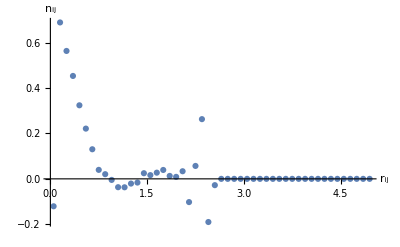

```mathematica
{σ,d,Ω,ntrial}={10,0,2,1};
cr=runEnsemble[d,σ,Ω,ntrial];
ListPlot[cr,Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15,PlotRange->All]
```

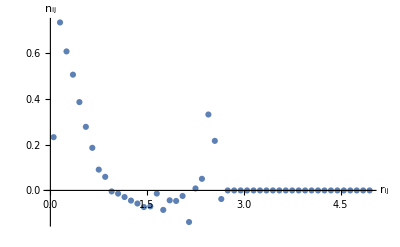

```mathematica
{σ,d,Ω,ntrial}={10,0,2,5};
cr=runEnsemble[d,σ,Ω,ntrial];
ListPlot[cr,Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15,PlotRange->All]
```

#### Play

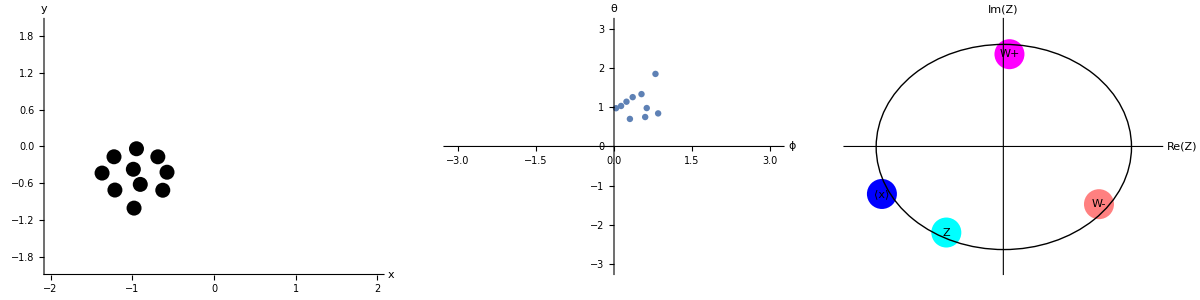

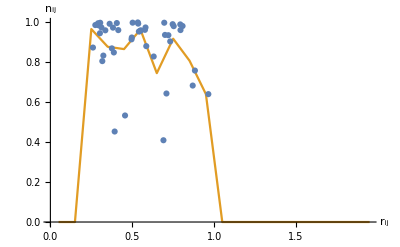

```mathematica
{σ,d,Ω}={10,0,1.2};
{znew,xs,ys,θs}=run[d,σ,Ω];
plotResults[znew,2]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,cr}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,cr},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

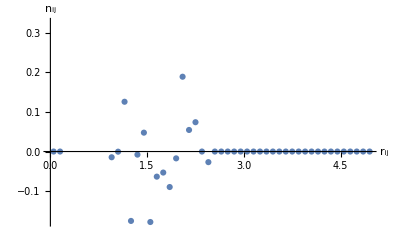

```mathematica
{σ,d,Ω}={10,0,1.2};
cr=runEnsemble[d,σ,Ω,2];
ListPlot[cr,Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

#### Strobe over Ω

```mathematica
data=ParallelTable[
{σ,d}={10,0};
{znew,xs,ys,θs}=run[d,σ,Ω];
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,cr}=findCthetathetaR[xs,ys,θs,t,n];
cr,
{Ω,0,2,0.5}
];
```

{{{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]}},{{0.0952432,0.993853},{0.149653,0.990909},{0.251931,0.988849},{0.350987,0.986961},{0.449823,0.985777},{0.548103,0.983306},{0.647375,0.980524},{0.747889,0.974383},{0.846761,0.965673},{0.943973,0.95182},{1.03983,0.92563},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]}},{{0.0981427,0.99764},{0.142187,0.989502},{0.247317,0.972281},{0.348793,0.946531},{0.449557,0.913612},{0.548854,0.872068},{0.648563,0.819432},{0.7493,0.747547},{0.84944,0.664283},{0.946759,0.54727},{1.04307,0.385297},{1.14641,0.186941},{1.24497,0.021223},{1.3404,-0.126569},{1.44705,-0.316669},{1.52654,-0.446432},{1.65829,-0.637027},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]}},{{0.0891595,0.437367},{0.158354,0.829954},{0.250771,0.736942},{0.352576,0.661233},{0.450958,0.510712},{0.547777,0.414995},{0.649575,0.28613},{0.748746,0.22118},{0.84788,0.132492},{0.950785,0.0484297},{1.04873,-0.0334484},{1.15074,-0.0951103},{1.24672,-0.165103},{1.34716,-0.195341},{1.44834,-0.267026},{1.54973,-0.252253},{1.64738,-0.297449},{1.74352,-0.340915},{1.84428,-0.208271},{1.94514,-0.190776},{2.04874,-0.113523},{2.14195,0.134066},{2.24307,0.314562},{2.35298,0.217895},{2.43804,0.272142},{2.53211,0.209351},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]}},{{0.0821581,0.146334},{0.160064,0.80113},{0.250039,0.612334},{0.353093,0.421762},{0.45031,0.330488},{0.548376,0.216114},{0.648431,0.114866},{0.752019,0.0141212},{0.848447,-0.0237489},{0.947482,-0.110433},{1.04897,-0.0809651},{1.14853,-0.0708206},{1.24814,-0.120963},{1.34795,0.00714531},{1.4462,-0.0289799},{1.55198,0.0405834},{1.65007,0.129924},{1.74877,-0.0606572},{1.84561,0.0158662},{1.94672,-0.17674},{2.04784,-0.155694},{2.14495,-0.197254},{2.2484,-0.0562801},{2.33579,-0.347283},{2.4005,0.999984},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]},{Mean[{}],Mean[{}]}}}

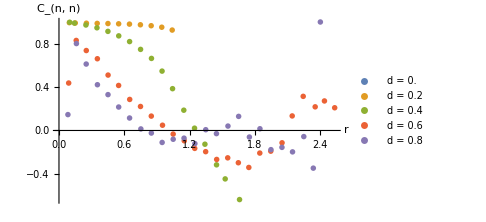

figures/sync-corr-phase-r-different-omega.png

```mathematica
p1=ListPlot[data,AxesLabel->{Style["r",17],Style["C_(n, n)",18]},PlotLegends->{Table["Ω = "<>ToString[d],{d,0,1,0.2}]},ImageSize->Medium,LabelStyle->14]
SetDirectory[NotebookDirectory[]];
Export["figures/sync-corr-phase-r-different-omega.png",p1]
```

## Develop

### Methods

```mathematica
findRijNij[xs_,ys_,θs_,t_,n_]:=Block[{dataRijNij,rij,nij,i,j},
dataRijNij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
AppendTo[dataRijNij,{rij,nij}]
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
];

clean[data_]:=Block[{cleanData,element,condition},
cleanData={};
For[i=1,i≤Length[data],i++,
element=data[[i]];
condition=NumberQ[element[[1]]]&&NumberQ[element[[2]]];
If[condition,AppendTo[cleanData,element]]
];
Return[cleanData]
]

findCthetathetaR[xs_,ys_,θs_,t_,n_]:=Block[{data,dr,rmax,binnedData,meanBinnedData,RijNijpairs},
RijNijpairs=findRijNij[xs,ys,θs,t,n]; (**)
dr=0.1;
rmax=Ceiling[Max[RijNijpairs[[All,1]]]]+1;
binnedData=BinLists[RijNijpairs,{0,rmax,dr},{0,1,1}];
meanBinnedData=Table[{binnedData[[i,1]][[All,1]]//Mean,binnedData[[i,1]][[All,2]]//Mean},{i,1,Length[binnedData]}];
meanBinnedData=clean[meanBinnedData];
Return[{RijNijpairs,meanBinnedData}]
];

run1[σ_,d_]:=Block[{dt,T,n,J,k,R,L,ω,z0,znew,t,NT,xs,ys,θs,x,y,θ},
{dt,T,n}={0.25,200,200};
{J,k}={1,1};
{R,L}={1,5};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];{x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
];
Return[{znew,xs,ys,θs}];
];
```

### Make code

Near to develop the two point phase correlation function C(θ,θ)(r)

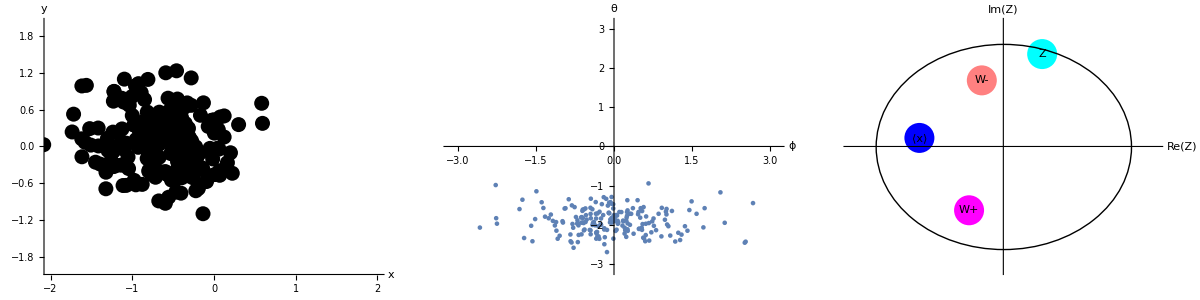

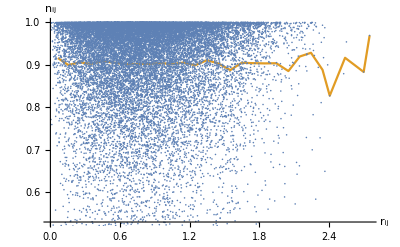

```mathematica
{σ,d}={10,0.5};
{znew,xs,ys,θs}=run1[σ,d];
plotResults[znew,2]
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,meanBinnedData}=findCthetathetaR[xs,ys,θs,t,n];
ListPlot[{RijNijpairs,meanBinnedData},Joined->{False,True},AxesLabel->{"r_ij","n_ij"},LabelStyle->15]
```

#### Vary d

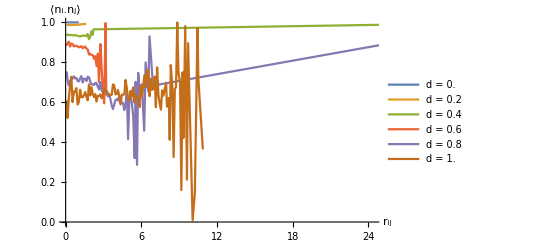

```mathematica
ds=ParallelTable[d,{d,0,1,0.2}];
data=Table[
{σ}={10};
{znew,xs,ys,θs}=run1[σ,d];
{t,n}={-1,Dimensions[xs][[2]]};
{RijNijpairs,meanBinnedData}=findCthetathetaR[xs,ys,θs,t,n];
meanBinnedData,
{d,ds}
];
ListPlot[data,AxesLabel->{"r_ij","⟨n_i.n_j⟩"},Joined->True,LabelStyle->15,PlotLegends->Table["d = "<>ToString[d],{d,ds}]]
```

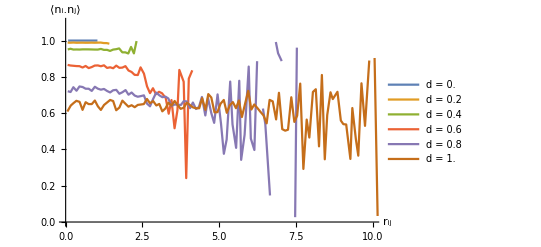

```mathematica
ListPlot[data,AxesLabel->{"r_ij","⟨n_i.n_j⟩"},Joined->True,LabelStyle->15,PlotLegends->Table["d = "<>ToString[d],{d,ds}],PlotRange->{{0,10},{0,1.1}}]
```

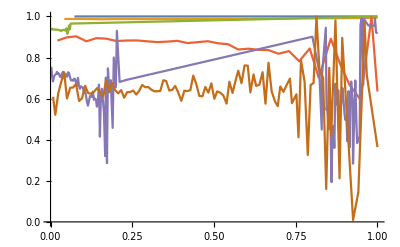

```mathematica
ListPlot[Table[{(data[[i]][[All,1]])/Max[data[[i]][[All,1]]],data[[i]][[All,2]]}ᵀ,{i,1,Length[data]}],Joined->True]
```

#### Average over ensembles

```mathematica
{σ,d}={10,0.5};
{znew,xs,ys,θs}=run1[σ,d];
{t,n}={-1,n=Dimensions[xs][[2]]};
{RijNijpairs,meanBinnedData}=findCthetathetaR[xs,ys,θs,t,n];
ntrial=5;
For[i=1,i<ntrial,i++,
{znew,xs,ys,θs}=run1[σ,d];
{RijNijpairs,meanBinnedData1}=findCthetathetaR[xs,ys,θs,t,n];
meanBinnedData=meanBinnedData+meanBinnedData1
]
```

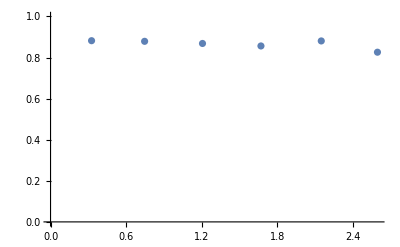

```mathematica
ListPlot[meanBinnedData/2,PlotRange->{0,1}]
```

## Functions

```mathematica
rhs=Compile[{{z,_Real,2},{n,_Integer},{J,_Real},{K,_Real},{σ,_Real},{ω,_Real,1}},
Module[{i,j,xji,yji,thetaji,inverseDistSq,distSq,dist,xtemp,ytemp,thetatemp,vel=ConstantArray[0.0,{3,n}]},
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
xji=z[[1,j]]-z[[1,i]];
yji=z[[2,j]]-z[[2,i]];
thetaji=z[[3,j]]-z[[3,i]];
distSq=xji^2+yji^2;
inverseDistSq=1/distSq;
dist=√distSq;
xtemp=xji((1 + J Cos[thetaji])/dist-inverseDistSq)HeavisideTheta[σ-dist];
ytemp=yji((1 + J Cos[thetaji])/dist-inverseDistSq)HeavisideTheta[σ-dist];
thetatemp=K*Sin[thetaji] /dist; 
vel[[1,i]]+=xtemp;vel[[1,j]]+=-xtemp;
vel[[2,i]]+=ytemp;vel[[2,j]]+=-ytemp;
vel[[3,i]]+=ω[[i]]+thetatemp;vel[[3,j]]+=ω[[j]]-thetatemp;
];
];
vel=vel/N[n];
vel
],
RuntimeAttributes->Listable,
Parallelization->True,
CompilationTarget->"C"
];


(*rhs[z_,n_,J_,K_,σ_,ω_,d_]:=Block[{noise,out},
If[d>0,
noise=d*RandomVariate[NormalDistribution[0,√dt],{3,n}],
noise=Table[0.0,{i,1,3},{j,1,n}]
];
out=rhsNoiseAux[z,n,J,K,σ,ω,noise];
Return[out]
];*)

findNoise[d_,n_,dt_]:=Block[{noise},
If[d>0,
noise=RandomVariate[NormalDistribution[0,√dt],{3,n}],
noise=Table[0.0,{i,1,3},{j,1,n}]
];
Return[noise];
]

euler[z_,F_,dt_,J_,K_,σ_,ω_,d_]:=Block[{znew,n,noise},
n=Dimensions[z][[2]];
noise=findNoise[d,n,dt];
Return[z+dt F[z,n,J,K,σ,ω]+d*noise]
];

rk4[z_,F_,dt_,J_,K_,σ_,ω_,d_]:=Block[{znew,n,i,j,k1,k2,k3,k4},
znew=ConstantArray[0,Dimensions[z]];
n=Dimensions[z][[2]];
k1=F[z,n,J,K,σ,ω,d];
k2=F[z+dt/2 k1,n,J,K,σ,ω,d];
k3=F[z+dt/2 k2,n,J,K,σ,ω,d];
k4=F[z+dt k3,n,J,K,σ,ω,d];
Return[z+dt/6(k1+2k2+2k3+k4)]
];

plotResults[z_,L_]:=Block[{colors,p1,p2,p3,Z,Wp,Wm,meanX,meanY,ϕ,θ,L1},
colors=ColorData["VisibleSpectrum"]/@((750-380)(Mod[z[[3,All]],2π]-1)/(2π)+380);
p1=Graphics[{PointSize[0.03],Point[{z[[1,All]],z[[2,All]]}ᵀ,VertexColors->colors]},
PlotRange->{{-L,L},{-L,L}},Axes->True,AspectRatio->1,ImageSize->Medium,AxesLabel->{"x","y"},LabelStyle->15];

ϕ=ArcTan[z[[1,All]],z[[2,All]]];
θ=z[[3,All]];
p2=ListPlot[{ϕ//mod,θ//mod}ᵀ,AxesLabel->{"ϕ","θ"},LabelStyle->15,PlotRange->{{-π,π},{-π,π}},ImageSize->Medium];

{Z,Wp,Wm}=findOrderPars[z];
{meanX,meanY}={Mean[z[[1,All]]],Mean[z[[2,All]]]};

L1=1.2;
p3=Graphics[{PointSize[0.06],
Cyan,Point[{Z//Re,Z//Im}],Black,Text["Z",{Z//Re,Z//Im}],
Magenta,Point[{Wp//Re,Wp//Im}],Black,Text["W+",{Wp//Re,Wp//Im}],
Pink,Point[{Wm//Re,Wm//Im}],Black,Text["W-",{Wm//Re,Wm//Im}],
Blue,Point[{meanX,meanY}],Black,Text["⟨x⟩",{meanX,meanY}],
Circle[{0,0},1]
},AxesOrigin->{0,0},PlotRange->{{-L1,L1},{-L1,L1}},Axes->True,Ticks->None,AspectRatio->1,AxesLabel->{"Re(Z)","Im(Z)"},LabelStyle->15,ImageSize->Medium];

Return[Grid[{{p1,p2,p3}}]];

];

findOrderPars[z_]:=Block[{Z,Wp,Wm,i,numOsc,ϕ,θ},
{Z,Wp,Wm}={0,0,0};
numOsc=Length[z[[1]]];
For[i=1,i≤numOsc,i++,
{ϕ,θ}={ArcTan[z[[1,i]],z[[2,i]]],z[[3,i]]};
Z+=Exp[ⅈ θ];
Wp+=Exp[ⅈ(ϕ+θ)];
Wm+=Exp[ⅈ(ϕ-θ)];;
];
Return[{Z/numOsc,Wp/numOsc,Wm/numOsc}]
];

mod[θ_]:=Return[Mod[θ,2π]-π];

findGamma[xs_,ys_]:=Block[{gamma,tolerance,phis,phi,s,temp,i,n},
n=Dimensions[xs][[2]];
gamma=0;
tolerance=0.05;
phis=ArcTan[xs,ys];
For[i=1,i≤n,i++,
phi=phis[[All,i]];
s=Sin[phi];
temp=(Max[s]-Min[s])/2;
If[temp>1-tolerance,gamma+=1];
];
Return[gamma/n]
];

findVelAutoCorr[xs_,ys_,n_,dt_]:=Block[{v,velAutoCorr},
velAutoCorr=Table[
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
{τ dt,Mean[Table[Normalize[v[[i,All,1]]].Normalize[v[[i,All,τ]]],{i,1,n}]]},
{τ,1,Length[xs]-1}
];
Return[velAutoCorr]
];

findV[xs_,ys_,dt_,n_]:=Block[{v},
v=Table[{Differences[xs[[All,i]]]/dt,Differences[ys[[All,i]]]/dt},{i,1,n}];
Return[v]
];

findRijVijPairs[v_,xs_,ys_,t_,n_]:=Block[{dataRijVij,rij,vij,i,j},
dataRijVij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
vij=Normalize[v[[i,All,t]]].Normalize[v[[j,All,t]]];
AppendTo[dataRijVij,{rij,vij}]
]
];
dataRijVij=Sort[dataRijVij];
Return[dataRijVij]
];

findCr[xs_,ys_,dt_,n_,t_]:=Block[{v,dataRijVij,rs,vs,groupedRs,groupedVs,k,binr,binv,i,j,Cr},
v=findV[xs,ys,dt,n];
dataRijVij=findRijVijPairs[v,xs,ys,t,n];

(*Parition values*)
{rs,vs}={dataRijVij[[All,1]],dataRijVij[[All,2]]};
groupedRs=BinLists[rs,{0,3,0.05}];
groupedVs={};
k=1;
For[i=1,i≤Length[groupedRs],i++,
binr=groupedRs[[i]];
binv={};
For[j=1,j≤Length[binr],j++,
AppendTo[binv,vs[[k]]];
k+=1;
];
AppendTo[groupedVs,binv]
];

(*Find averages values*)
Cr=Table[
{Mean[groupedRs[[i]]],Mean[groupedVs[[i]]]},
{i,1,Length[groupedRs]}
];
Return[Cr]
];

findGr[xs_,ys_,n_,t_]:=Block[{i,j,rijs,rij,rs,gs,dr,rmax},
(* Find g(r) := radial density *)

(*Find pairwise rij*)
rijs={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
AppendTo[rijs,rij]
]
];

(*Radial density*)
{dr,rmax}={0.1,2};
rs=Table[i,{i,0.05,rmax,dr}];
gs=BinLists[rijs,{0,rmax,dr}];
gs=Table[Length[gs[[i]]]/(n(n-1))//N,{i,1,Length[gs]}];

Return[{rs,gs}]
];

findVelAutoCorr[xs_,ys_,dt_,NT_]:=Block[{vx,vy,v,tcutoff,c},
vx=Table[Differences[xs[[All,i]]]/dt,{i,1,n}];
vy=Table[Differences[ys[[All,i]]]/dt,{i,1,n}];
v=Table[{vx[[i]],vy[[i]]}ᵀ,{i,1,n}];
tcutoff=Round[0.5*NT];
c=Table[
{t dt,Sum[Normalize[v[[i,tcutoff]]].Normalize[v[[i,t]]],{i,1,n}]/n},
{t,tcutoff,NT-1}
];
Return[c]
];

findRijNij[xs_,ys_,θs_,t_,n_]:=Block[{dataRijNij,rij,nij,i,j},
dataRijNij={};
(*Iterate over all pairs*)
For[i=1,i≤n,i++,
For[j=i+1,j≤n,j++,
rij=((xs[[t,i]]-xs[[t,j]])^2+(ys[[t,i]]-ys[[t,j]])^2)^(1/2);
nij={Cos[θs[[t,i]]],Sin[θs[[t,i]]]}.{Cos[θs[[t,j]]],Sin[θs[[t,j]]]};
AppendTo[dataRijNij,{rij,nij}]
]
];
dataRijNij=Sort[dataRijNij];
Return[dataRijNij]
];

clean[data_]:=Block[{cleanData,element,condition},
cleanData={};
For[i=1,i≤Length[data],i++,
element=data[[i]];
condition=NumberQ[element[[1]]]&&NumberQ[element[[2]]];
If[condition,AppendTo[cleanData,element]]
];
Return[cleanData]
]

findCthetathetaR[xs_,ys_,θs_,t_,n_]:=Block[{data,dr,rmax,binnedData,meanBinnedData,RijNijpairs},
RijNijpairs=findRijNij[xs,ys,θs,t,n]; (**)
dr=0.1;
rmax=Ceiling[Max[RijNijpairs[[All,1]]]]+1;
binnedData=BinLists[RijNijpairs,{0,rmax,dr},{-1,1,2}];
meanBinnedData=Table[{binnedData[[i,1]][[All,1]]//Mean,binnedData[[i,1]][[All,2]]//Mean},{i,1,Length[binnedData]}];
(*meanBinnedData=clean[meanBinnedData];*)
Return[{RijNijpairs,meanBinnedData}]
];

run1[σ_,d_]:=Block[{dt,T,n,J,k,R,L,ω,z0,znew,t,NT,xs,ys,θs,x,y,θ},
{dt,T,n}={0.25,200,300};
{J,k}={1,1};
{R,L}={1,5};
ω=Table[0,{i,1,n}];
z0=Table[{RandomReal[{-L,L}],RandomReal[{-L,L}],RandomReal[{-π,π}]},{j,1,n}]ᵀ;
znew=ConstantArray[0,{3,n}];
{t,NT}={0,Round[T/dt]};
{xs,ys,θs}={{},{},{}};
While[t<NT,
znew=euler[z0,rhs,dt,J,k,σ,ω,d];{x,y,θ}=znew;
z0=znew;t++;AppendTo[xs,x];AppendTo[ys,y];AppendTo[θs,θ];
];
Return[{znew,xs,ys,θs}];
];
```